## Puntos equiespaciados en una línea

```mathematica
GoogleMapsMarcadores=Import["/home/jadeleon/Documents/transmetro/marcadores_bulevar_sancris.csv"][[2;;,{3,4}]]
```

{{14.5951,-90.5674},{14.5954,-90.5684},{14.5952,-90.57},{14.5931,-90.5716},{14.592,-90.5744},{14.5903,-90.5747},{14.5901,-90.5756},{14.5931,-90.5788},{14.5978,-90.5784},{14.599,-90.5789},{14.6079,-90.5869},{14.6088,-90.588},{14.6093,-90.5895},{14.6095,-90.594},{14.6101,-90.5946},{14.6115,-90.5951},{14.6122,-90.5959},{14.6124,-90.5985},{14.6138,-90.6006},{14.6135,-90.6031},{14.6142,-90.6049},{14.6147,-90.6053},{14.6161,-90.6053},{14.6175,-90.6062}}

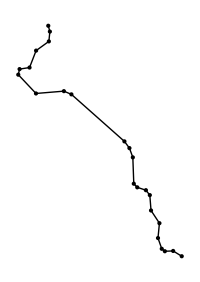

```mathematica
Graphics[{Line[#],PointSize[Large],Point[#]}&[GoogleMapsMarcadores],ImageSize->200]
```

Ahora quiero generar

```mathematica
DistanciaEntrePuntos=MapThread[EuclideanDistance,{#,RotateLeft[#]}&[GoogleMapsMarcadores]][[;;-2]]
```

{0.00101651,0.00165873,0.00264237,0.00305491,0.00169012,0.000965401,0.00433665,0.00469622,0.00137084,0.0118996,0.00140801,0.00166087,0.00443289,0.000841724,0.00152738,0.00106042,0.00258774,0.00256275,0.00251149,0.00191651,0.000662193,0.0013909,0.00169336}

```mathematica
NumeroDePuntos={};
Do[
n=1;While[Abs[Round[#,10.^0]-Round[#,10.^-2]]&[DistanciaEntrePuntos[[1]]/DistanciaEntrePuntos[[i]]*n]>=0.1,n++];
AppendTo[NumeroDePuntos,n]
,{i,Length[DistanciaEntrePuntos]}]
NumeroDePuntos=NumeroDePuntos-1
```

{0,4,4,2,4,0,3,4,3,0,6,4,3,4,2,0,4,4,4,1,1,3,4}

```mathematica
EspaciamientoEntrePuntosVecinos=ReplaceAll[DistanciaEntrePuntos/(NumeroDePuntos+1),ComplexInfinity->0]
```

{0.00101651,0.000331747,0.000528473,0.0010183,0.000338024,0.000965401,0.00108416,0.000939244,0.00034271,0.0118996,0.000201145,0.000332175,0.00110822,0.000168345,0.000509128,0.00106042,0.000517548,0.00051255,0.000502299,0.000958254,0.000331097,0.000347725,0.000338673}

```mathematica
VectoresEnLaDireccionPuntoVecino=Normalize/@(#-RotateRight[#]&[GoogleMapsMarcadores][[2;;]])
```

{{0.265614,-0.96408},{-0.102488,-0.994734},{-0.80988,-0.586595},{-0.360076,-0.932923},{-0.988096,-0.153835},{-0.227884,-0.973688},{0.684861,-0.728674},{0.996546,0.0830455},{0.919145,-0.393919},{0.747085,-0.664729},{0.596585,-0.80255},{0.343193,-0.939265},{0.0360938,-0.999348},{0.689062,-0.724703},{0.949336,-0.314263},{0.622392,-0.782705},{0.0772875,-0.997009},{0.55019,-0.83504},{-0.0955607,-0.995424},{0.328723,-0.944426},{0.785269,-0.619155},{0.999354,0.035948},{0.850378,-0.526172}}

```mathematica
PuntosFinales=Flatten[Table[GoogleMapsMarcadores[[n]]+i*EspaciamientoEntrePuntosVecinos[[n]]*VectoresEnLaDireccionPuntoVecino[[n]],{n,Length[NumeroDePuntos]},{i,0,NumeroDePuntos[[n]]}],1]
```

{{14.5951,-90.5674},{14.5954,-90.5684},{14.5954,-90.5687},{14.5953,-90.569},{14.5953,-90.5694},{14.5953,-90.5697},{14.5952,-90.57},{14.5948,-90.5703},{14.5944,-90.5707},{14.594,-90.571},{14.5935,-90.5713},{14.5931,-90.5716},{14.5927,-90.5725},{14.5924,-90.5735},{14.592,-90.5744},{14.5917,-90.5745},{14.5913,-90.5745},{14.591,-90.5746},{14.5907,-90.5746},{14.5903,-90.5747},{14.5901,-90.5756},{14.5909,-90.5764},{14.5916,-90.5772},{14.5923,-90.578},{14.5931,-90.5788},{14.594,-90.5787},{14.595,-90.5786},{14.5959,-90.5786},{14.5968,-90.5785},{14.5978,-90.5784},{14.5981,-90.5785},{14.5984,-90.5787},{14.5987,-90.5788},{14.599,-90.5789},{14.6079,-90.5869},{14.608,-90.587},{14.6082,-90.5872},{14.6083,-90.5873},{14.6084,-90.5875},{14.6085,-90.5877},{14.6086,-90.5878},{14.6088,-90.588},{14.6089,-90.5883},{14.609,-90.5886},{14.6091,-90.5889},{14.6092,-90.5892},{14.6093,-90.5895},{14.6094,-90.5906},{14.6094,-90.5918},{14.6094,-90.5929},{14.6095,-90.594},{14.6096,-90.5941},{14.6097,-90.5942},{14.6098,-90.5943},{14.6099,-90.5945},{14.6101,-90.5946},{14.6105,-90.5947},{14.611,-90.5949},{14.6115,-90.5951},{14.6122,-90.5959},{14.6122,-90.5964},{14.6123,-90.5969},{14.6123,-90.5974},{14.6123,-90.598},{14.6124,-90.5985},{14.6127,-90.5989},{14.6129,-90.5993},{14.6132,-90.5998},{14.6135,-90.6002},{14.6138,-90.6006},{14.6137,-90.6011},{14.6137,-90.6016},{14.6136,-90.6021},{14.6136,-90.6026},{14.6135,-90.6031},{14.6139,-90.604},{14.6142,-90.6049},{14.6144,-90.6051},{14.6147,-90.6053},{14.615,-90.6053},{14.6154,-90.6053},{14.6157,-90.6053},{14.6161,-90.6053},{14.6164,-90.6055},{14.6167,-90.6056},{14.6169,-90.6058},{14.6172,-90.606}}

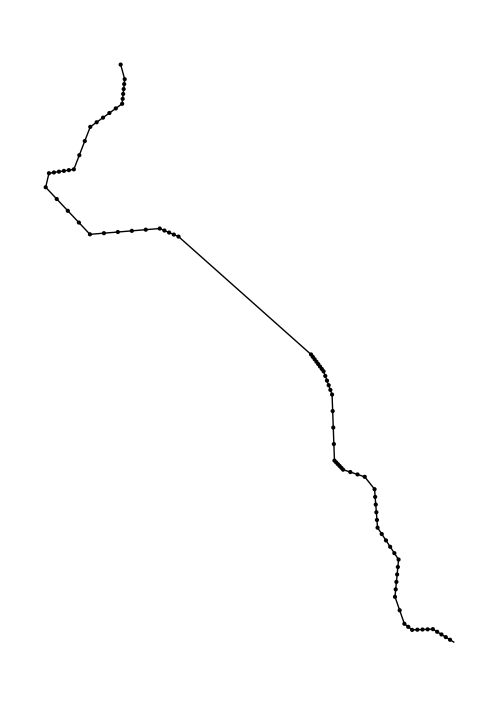

```mathematica
Graphics[{Line[GoogleMapsMarcadores],PointSize[Large],Point[#]}&[Sort[PuntosFinales]],ImageSize->500]
```

```mathematica
RandomNumbers=Round[#,10.^-2]&/@RandomReal[{0,1},10]
```

{0.5,0.61,0.92,0.01,0.68,0.05,0.84,0.04,0.68,0.07}

```mathematica
Min[RandomNumbers]
```

0.06

```mathematica
(*Function to convert degrees to radians*)degreesToRadians[degrees_]:=degrees*Pi/180;

(*Haversine function to compute distance*)
haversine[θ_]:=Sin[θ/2]^2;

(*Distance calculation function*)
distance[{lat1_,lon1_},{lat2_,lon2_}]:=Module[{earthRadius=6371},With[{dLat=degreesToRadians[lat2-lat1],dLon=degreesToRadians[lon2-lon1]},2*earthRadius*ArcSin[Sqrt[haversine[dLat]+Cos[degreesToRadians[lat1]]*Cos[degreesToRadians[lat2]]*haversine[dLon]]]]]

(*Example usage*)
point1={53.349805,-6.26031}; (*Dublin,Ireland*)
point2={40.712776,-74.005974}; (*New York City,USA*)

distanceBetweenPoints=distance[point1,point2];
Print["Distance between points: ",distanceBetweenPoints," km"];
```

Distance between points: 5114.88 km

```mathematica
distance[GoogleMapsMarcadores[[1]],GoogleMapsMarcadores[[2]]]
```

0.109645

```mathematica
EuclideanDistance[GoogleMapsMarcadores[[1]],GoogleMapsMarcadores[[2]]]
```

0.00101651

```mathematica
MarcadoresBulevarSanCris=GeoPosition/@GoogleMapsMarcadores
```

{GeoPosition[{14.5951,-90.5674}],GeoPosition[{14.5954,-90.5684}],GeoPosition[{14.5952,-90.57}],GeoPosition[{14.5931,-90.5716}],GeoPosition[{14.592,-90.5744}],GeoPosition[{14.5903,-90.5747}],GeoPosition[{14.5901,-90.5756}],GeoPosition[{14.5931,-90.5788}],GeoPosition[{14.5978,-90.5784}],GeoPosition[{14.599,-90.5789}],GeoPosition[{14.6079,-90.5869}],GeoPosition[{14.6088,-90.588}],GeoPosition[{14.6093,-90.5895}],GeoPosition[{14.6095,-90.594}],GeoPosition[{14.6101,-90.5946}],GeoPosition[{14.6115,-90.5951}],GeoPosition[{14.6122,-90.5959}],GeoPosition[{14.6124,-90.5985}],GeoPosition[{14.6138,-90.6006}],GeoPosition[{14.6135,-90.6031}],GeoPosition[{14.6142,-90.6049}],GeoPosition[{14.6147,-90.6053}],GeoPosition[{14.6161,-90.6053}],GeoPosition[{14.6175,-90.6062}]}

```mathematica
GeoDistance[MarcadoresBulevarSanCris]
```

6.2786 km

```mathematica
6278.6/100
```

62.786